# FelipeBarbosa/SymDALI

Implementation of the DALI algorithm (Derivative Approximation for LIkelihoods) for gravitational wave likelihoods

## Paclet Manifest

"Assets"

"ASD"

"18213_ET10kmcolumns.txt"AssetsASD18213_ET10kmcolumns.txt

"18213_ET15kmcolumns.txt"AssetsASD18213_ET15kmcolumns.txt

"18213_ET20kmcolumns.txt"AssetsASD18213_ET20kmcolumns.txt

"AplusDesign.txt"AssetsASDAplusDesign.txt

"avirgo_O5low_NEW.txt"AssetsASDavirgo_O5low_NEW.txt

"cosmic_explorer_20km_pm_strain.txt"AssetsASDcosmic_explorer_20km_pm_strain.txt

"cosmic_explorer_20km_strain.txt"AssetsASDcosmic_explorer_20km_strain.txt

"cosmic_explorer_40km_lf_strain.txt"AssetsASDcosmic_explorer_40km_lf_strain.txt

"cosmic_explorer_strain.txt"AssetsASDcosmic_explorer_strain.txt

"ET-0000A-18_ETDSensitivityCurveTxtFile.txt"AssetsASDET-0000A-18_ETDSensitivityCurveTxtFile.txt

"kagra_80Mpc.txt"AssetsASDkagra_80Mpc.txt

"Derivatives"

"Detectors"

"Defs.mx"AssetsDerivativesDetectorsDefs.mx

"Defs.wdx"AssetsDerivativesDetectorsDefs.wdx

"IMRPhenomD"

"Defs.mx"AssetsDerivativesIMRPhenomDDefs.mx

"Defs.wdx"AssetsDerivativesIMRPhenomDDefs.wdx

"IMRPhenomHM"

"Defs.mx"AssetsDerivativesIMRPhenomHMDefs.mx

"Defs.wdx"AssetsDerivativesIMRPhenomHMDefs.wdx

"Documentation"

"Kernel"

"DALICoefficients.wl"KernelDALICoefficients.wl

"DALIPolynomial.wl"KernelDALIPolynomial.wl

"DerivativeTools.wl"KernelDerivativeTools.wl

"Detectors.wl"KernelDetectors.wl

"Population.wl"KernelPopulation.wl

"SymDALI.wl"KernelSymDALI.wl

"Utils.wl"KernelUtils.wl

"LICENSE"LICENSE

"PacletInfo.wl"PacletInfo.wl

"SymDALI | Definition Notebook.nb"SymDALI | Definition Notebook.nb

## Web Content

### Headline Image



### Basic Description

This paclet provides the Wolfram Language components of the SymDALI framework, a hybrid Python–Wolfram Language framework for gravitational-wave parameter estimation using Fisher and DALI (Derivative Approximation of LIkelihoods) approximations.

### Details

The official docummentation links are available on the GitHub page: https://github.com/Felipe-4/SymDALI

### Primary Context

FelipeBarbosa`SymDALI`

### Main Guide Page

## Examples

### Initialization for Examples

```mathematica
PacletDirectoryLoad["/Users/felipe/Documents/GitHub/SymDALI/WolframLanguage/SymDALI"];
```

```mathematica
Needs["FelipeBarbosa`SymDALI`"];
```

### Basic Examples

We can calculate the plus and cross polarizations of the IMRPhenomHM waveform:

```mathematica
f = Range[5,1024,0.25];
Mc = 20;
q=0.9;
s1z= 0.1; s2z=-0.3;
iota = π;
tc = 0;
phiRef = π/3;
dL = 3;
{hp,hc} = hphcIMRPhenomHM[f, Mc, q, s1z, s2z, iota, tc, phiRef, 1/dL];
```

So we can check the real and imaginary part of the plus polarization

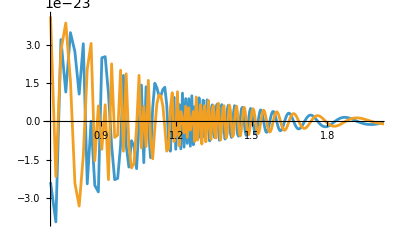

```mathematica
ListLinePlot[
{Re@hp, Im@hp},
PlotRange->{{5,100}, All},
DataRange->{5, 1024},
ScalingFunctions->{"Log10", None}
]
```

### Scope

You can calculate the Fisher matrix for a network of Einstein telescope detectors with the IMRPhenomHM waveform

```mathematica
fp=<|"dec"->-0.883787,"phi"->6.18412,"psi"->0.471846,"Mc"->190.258,"q"->0.935815,"s1z"->0.107562,"s2z"->-0.0254365,"iota"->2.60021,"invdL"->0.0284797,"tc"->61093.87906420612,"phiRef"->5.93578|>;

ET1=<|"Position"->DetectorVertex["ET-S"],"DetectorTensor"->DetectorTensor["ET-S-L"],"ASD"->ASD["ET-15-lfhf"]|>;

ET2=<|"Position"->DetectorVertex["ET-MR"],"DetectorTensor"->DetectorTensor["ET-MR-L-45"],"ASD"->ASD["ET-15-lfhf"]|>;

FM = DALITensors["IMRPhenomHM",fp,{ET1,ET2},1];
```

"pre work"  0.000035

"parsing NRules"  0.000044

"MakeDefs"  0.001576

0.000141

"FpFc"  0.013694

"hphc"  0.600351

"Redefine labels"  0.001114

"Gradient Recombination"  0.001354

"extra cleaning"  0.000012

"DALIList"  0.002867

We reshape it into the usual form of a matrix and invert it:

```mathematica
FM2=ArrayReshape[FM,{11,11}];
{Cov,epsilon}=CholeskyInverse[FM2];
```

epsilon gives the difference between the product of the Fisher and Covariance with respect to the identity matrix:

```mathematica
epsilon == Max[Join[
Cov.FM2- IdentityMatrix[11], FM2.Cov-IdentityMatrix[11]
]//Abs]
```

True

The relation between matrix dimensions and waveform variables can be obtained with EmptyAssociation:

```mathematica
EmptyAssociation["Aligned"]
```

<|dec→1,phi→2,psi→3,Mc→4,q→5,s1z→6,s2z→7,iota→8,invdL→9,tc→10,phiRef→11|>

## Source & Additional Information

### Creator

Felipe Barbosa

### Source Control Repository

https://github.com/Felipe-4/SymDALI

### License

MIT License [»](https://resources.wolframcloud.com/PacletRepository/licenses/MIT)
 Apache License 2.0 [»](https://resources.wolframcloud.com/PacletRepository/licenses/Apache-2.0)
 Creative Commons Zero v1.0 Universal [»](https://resources.wolframcloud.com/PacletRepository/licenses/CC0-1.0)
 NoneA license is not required for personal deployments

### Keywords

Fisher

DALI

Gravitational waves

### Categories

Cloud & Deployment
 Data Manipulation & Analysis
 External Interfaces & Connections
 Geographic Data & Computation
 Graphs & Networks
 Images
 Machine Learning
 Scientific and Medical Data & Computation
 Sound & Video
 Symbolic & Numeric Computation
 Time-Related Computation
 Visualization & Graphics |  Core Language & Structure
 Engineering Data & Computation
 Financial Data & Computation
 Geometry
 Higher Mathematical Computation
 Knowledge Representation & Natural Language
 Notebook Documents & Presentation
 Social, Cultural & Linguistic Data
 Strings & Text
 System Operation & Setup
 User Interface Construction

### Related Resource Objects

Resource Name (resources from any Wolfram repository)

### Original Source References and Attributions

Source, reference or citation

### Links

Link to other related material

### Compatibility

#### Wolfram Language Version

14.1+

#### Operating System

Windows |  Mac |  Linux

#### Environments

SessionLocal or cloud interactive session
 WebEvaluationCloud evaluation initiated by an HTTP request
 BatchJobRemote batch job |  ScriptScript run in batch mode
 WebAPIAPI called through an HTTP request
 |  SubkernelParallel or grid subkernel
 ScheduledScheduled task

#### Cloud Support

Supported in cloud

#### Required Features

Notebooks |  Parallel Kernels |  Cloud Access

### Disclosures

Local filesDisclosuresLocalFilesChoose this option if your paclet directly does any of the following during loading or normal usage:
◼ Creates, deletes or modifies local files
◼ Imports data from local files
File operations related to normal paclet installation and loading are excepted.Click for more information

Wolfram accountDisclosuresWolframAccountChoose this option if your paclet directly does any of the following:
◼ Requires, uses, or records any information related to user’s Wolfram ID
◼ Interacts with the user’s Cloud account or Wolfram account
◼ Creates, deletes or modifies the user’s cloud objects
◼ Creates or executes cloud deployed scheduled tasks
◼ Uses cloud credits, service credits or Wolfram credits
◼ Makes WolframAlpha callsClick for more information

External servicesDisclosuresExternalServicesChoose this option if your paclet directly does any of the following:
◼ Makes requests to external services (http, ftp, ssh, etc)
◼ Creates or uses service connection
◼ Send emailsClick for more information

Wolfram Language system configurationDisclosuresWLSystemConfigurationChoose this option if your paclet directly does any of the following:
◼ Creates persistent local scheduled tasks
◼ Modifies WL system or environment settings
◼ Modifies $Path, Directory, or similar
◼ Installs additional paclets or dependencies
◼ Creates or imports non-public ResourceObject content
◼ Makes FrontEnd modifications
◼ Internal handlersClick for more information

Wolfram Language built-in symbolsDisclosuresWLSystemSymbolsChoose this option if your paclet directly modifies definitions of built-in symbols such as those in System` or other internal contexts.Click for more information

Paclet dependenciesDisclosuresPacletDependenciesChoose this option if your paclet directly installs or updates any additional paclets. Paclets that are included with the Wolfram system do not require a disclosure.Click for more information

OS configurationDisclosuresOSConfigurationChoose this option if your paclet directly does any of the following:
◼ Modifies OS settings
◼ Makes any use of SystemCredentialClick for more information

Local system interactionsDisclosuresLocalSystemInteractionsChoose this option if your paclet directly does any of the following:
◼ Executes Shell or RUN commands
◼ Uses external evaluators via ExternalEvaluate
◼ Interacts with external libraries
◼ Reads or writes to streams or sockets
◼ Launches parallel kernels, subkernels or GPUsClick for more information

OtherDisclosuresOtherAdd additional text as needed in a new cell below to document any additional disclosures that are not listed above.Click for more information

## Author Notes

The present version can calculate DALI tensors only up to derivative order 4 and does not include the Earth's rotation.